```mathematica
Clear["Global`*"]
```

## Initial Value

```mathematica
L=8;(*km*)
bit=25;
λ=1.55*10^-6;(*m*)
d=16;(*ps/km・nm*)
c=3*10^8;
β2=d/(2*Pi*c)λ^2*10^-3;
nm=3.96;(*電気信号の実効屈折率*)
ng=2.19;(*光波の群屈折率*)
c=3*10^8;
y=38.25*10^-3;(*mm*)
t[l_]:=l/c*(nm+ng);(*s*)
total=t[y];
initial=1000;
pitch=50*10^-6;(*um*)
pitchmm=pitch*10^3;
Δt=pitch*(nm+ng)/(3*10^8);
sumw=(total+Δt*initial)/Δt  ;
polnumber=1+IntegerPart[sumw]-initial;
electrodelength=N[pitch*polnumber];
electrodelengthmm=electrodelength*10^3;
Print[β2,"ps^2/km"]
Print[total*10^12,"ps"]
Print[Δt*10^12,"ps"]
Print[sumw,"point"]
Print["Rev pattern is", polnumber,"point"]
Print["electrodelength is",electrodelength*10^3,"mm"]
Print[electrodelengthmm,"mm"]
```

2.03931×10^-23ps^2/km

784.125ps

1.025ps

1765.point

Rev pattern is765point

electrodelength is38.25mm

38.25mm

## Product Random NRZ Signal

{0,1,0,1,1,0,1,1,1,0,0,0,1,0,0,1,0,0,1,1,0,1,1,1,1}

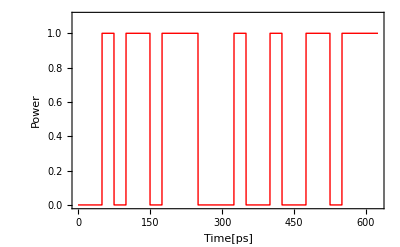

```mathematica
(*For[i=1;j=0,i≤bit,i++,
For[m=j;random=RandomChoice[{0,1}],j≤m+1,j=j+1,digital[j]=random]]

rm=Table[digital[t],{t,1,bit}]*)
digital[1]=0;
digital[2]=1;
digital[3]=0;digital[4]=1;digital[5]=1;digital[6]=0;digital[7]=1;digital[8]=1;digital[9]=1;digital[10]=0;digital[11]=0;digital[12]=0;digital[13]=1;digital[14]=0;digital[15]=0;digital[16]=1;digital[17]=0;digital[18]=0;digital[19]=1;digital[20]=1;digital[21]=0;digital[22]=1;digital[23]=1;digital[24]=1;digital[25]=1;

rm=Table[digital[t],{t,1,bit}]
step1[t_,i_]:=If[digital[i]==1,If[i*25*10^-12<t<(i+1)*25*10^-12,1,0],If[i*25*10^-12<t<(i+1)*25*10^-12,0,0]]
signal[t_]:=signal[t]=∑_(i=1)^bit step1[t,i]
Plot[signal[t*10^-12],{t,0,bit*25},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ps]","Power"},BaseStyle->{Bold,FontSize->20},PlotRange->{0,1.1}]
```

```mathematica
Fc= 200 *10^12;(*搬送波の周波数[THz]*)
carrier[t]= (Cos[2*Pi*Fc*t]+1)/2
Plot[carrier[t], {t,0,600}]
cs[t_]=signal[t]*carrier[t]
```

1/2 (1+Cos[400000000000000 π t])

-Graphics-

1/2 (1+Cos[400000000000000 π t]) (If[1/40000000000<t<1/20000000000,0,0]+If[1/20000000000<t<3/40000000000,1,0]+If[3/40000000000<t<1/10000000000,0,0]+If[1/10000000000<t<1/8000000000,1,0]+If[1/8000000000<t<3/20000000000,1,0]+If[3/20000000000<t<7/40000000000,0,0]+If[7/40000000000<t<1/5000000000,1,0]+If[1/5000000000<t<9/40000000000,1,0]+If[9/40000000000<t<1/4000000000,1,0]+If[1/4000000000<t<11/40000000000,0,0]+If[11/40000000000<t<3/10000000000,0,0]+If[3/10000000000<t<13/40000000000,0,0]+If[13/40000000000<t<7/20000000000,1,0]+If[7/20000000000<t<3/8000000000,0,0]+If[3/8000000000<t<1/2500000000,0,0]+If[1/2500000000<t<17/40000000000,1,0]+If[17/40000000000<t<9/20000000000,0,0]+If[9/20000000000<t<19/40000000000,0,0]+If[19/40000000000<t<1/2000000000,1,0]+If[1/2000000000<t<21/40000000000,1,0]+If[21/40000000000<t<11/20000000000,0,0]+If[11/20000000000<t<23/40000000000,1,0]+If[23/40000000000<t<3/5000000000,1,0]+If[3/5000000000<t<1/1600000000,1,0]+If[1/1600000000<t<13/20000000000,1,0])

```mathematica
∫_0^(bit*25*10^-12) cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1
```

-((ⅈ ⅇ^(-(ⅈ f π)/800000000) (-1+ⅇ^((ⅈ f π)/20000000000)) (1+ⅇ^((ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/10000000000)+ⅇ^((ⅈ f π)/5000000000)+ⅇ^((ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/2500000000)+ⅇ^((11 ⅈ f π)/20000000000)+ⅇ^((3 ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/1250000000)+ⅇ^((17 ⅈ f π)/20000000000)+ⅇ^((19 ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/1000000000)+ⅇ^((11 ⅈ f π)/10000000000)) (-20000000000000000000000000000+f^2))/(2 f (-40000000000000000000000000000+f^2) π))

```mathematica
fc[f_]:=-((ⅈ ⅇ^(-(ⅈ f π)/800000000) (-1+ⅇ^((ⅈ f π)/20000000000)) (1+ⅇ^((ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/10000000000)+ⅇ^((ⅈ f π)/5000000000)+ⅇ^((ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/2500000000)+ⅇ^((11 ⅈ f π)/20000000000)+ⅇ^((3 ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/1250000000)+ⅇ^((17 ⅈ f π)/20000000000)+ⅇ^((19 ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/1000000000)+ⅇ^((11 ⅈ f π)/10000000000)) (-20000000000000000000000000000+f^2))/(2 f (-40000000000000000000000000000+f^2) π))
```

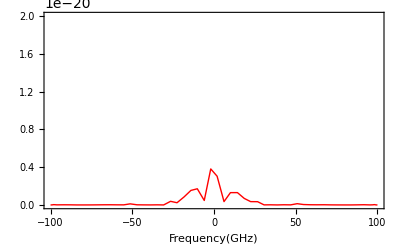

```mathematica
Plot[(Re[fc[f*10^9]]^2+Im[fc[f*10^9]]^2),{f,-1*^2,1*^2},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(GHz)"},BaseStyle->{Bold,FontSize->15},PlotRange->{0,20*10^-21}]
```

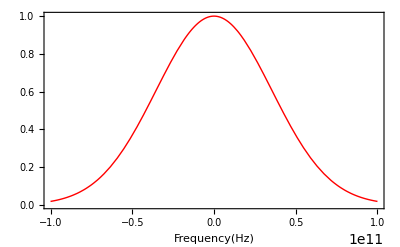

```mathematica
mado[f_]:=ⅇ^(-(f*10^-10.7)^2)
Plot[mado[f],{f,-100*10^9,100*10^9},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(Hz)",},BaseStyle->{Bold,FontSize->15}]
```

```mathematica
For[i=1,i≤1200,i++,sinsper1[i]=Re[fc[i*10^8]]*mado[i*10^8]]       
For[i=1,i≤1200,i++,sinspei1[i]=Im[fc[i*10^8]]*mado[i*10^8]]       
sig[t_]:=sig[t]=(∑_(i=1)^1200 sinsper1[i]*Cos[2*Pi*i*10^8*t]+∑_(i=1)^1200 sinspei1[i]*Sin[-2*Pi*i*10^8*t])
```

```mathematica
minnrz=-MinValue[sig[x1*10^-12],x1];
maxnrz=MaxValue[sig[x]+minnrz,x];
nrzsig[t_]:=(sig[t]+minnrz)/maxnrz;
```

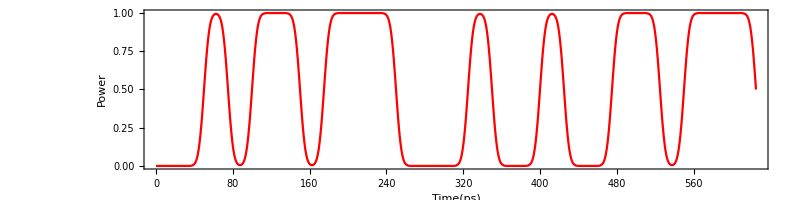

```mathematica
Plot[nrzsig[t*10^-12],{t,0,bit*25},Frame->True,FrameLabel->{"Time(ps)","Power"},PlotStyle->{Red},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

## Function for Compensation Fiber Dispersion

```mathematica
(*f[x_]:=1/2(1/(√(2*Pi*β2*60))*10^6*Exp[+ⅈ*(((t[x]*10^-3)^2)/(2*β2*60)-Pi/4)]+

1/(√(2*Pi*β2*80))*10^6*Exp[+ⅈ*(((t[x]*10^-3)^2)/(2*β2*80)-Pi/4)]);*)
```

```mathematica
(*FindMaximum[{Re@f[x1],{0<x1<10}},{x1,3}]*)
```

```mathematica
(*max=9.87972350691273*^15;
Plot[Re@f[l]/max,{l,-electrodelengthmm/2,electrodelengthmm/2},Frame->True,FrameLabel->{"Length(mm)","Real Part"}]*)
```

## Impulse Responce for Fiber Dispersion

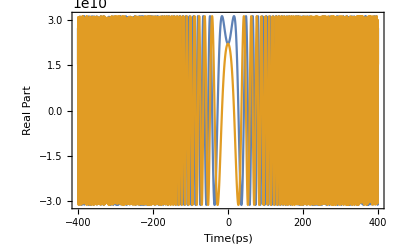

```mathematica
hdis[t_]:=1/(√(2*Pi*β2*L))*Exp[-ⅈ*(t^2/(2*β2*L)-Pi/4)];(*Impluse ver.time*)
(*FindMaximum[{Re@hdis[x1],{0<x1<10}},{x1,3}]
max=9.876974769287008*^15;*)
Plot[{Re@hdis[t*10^-12],Im@hdis[t*10^-12]},{t,-400,400},Frame->True,FrameLabel->{"Time(ps)","Real Part"}]
```

## Impulse Responce for CompensationDispersion

```mathematica
(*hcmp[t_]:=1/2(1/(√(2*Pi*β2*60))*10^6*Exp[+ⅈ*(t^2/(2*β2*60)-Pi/4)]+

1/(√(2*Pi*β2*80))*10^6*Exp[+ⅈ*(t^2/(2*β2*80)-Pi/4)]);*)
```

```mathematica
(*Plot[{Re@hcmp[t*10^-12],Im@hcmp[t*10^-12]},{t,-400,400},Frame->True,FrameLabel->{"Time(ps)","Real Part"}]*)
```

## Sampling

```mathematica
samp=0.5;(*sampling number*)
```

```mathematica
bound=IntegerPart[total*10^12];
```

```mathematica
(*For[i=-100000,i≤-bound/2,i=i+samp,hcmp2[i]=0]
For[j=0;i=-bound/2,i≤bound/2,i=i+samp;j=j+samp,hcmp2[i]=hcmp[j*10^-12]]
For[i=bound/2,i≤100000,i=i+samp,hcmp2[i]=0]*)
```

```mathematica
(*IntegerPart[total*10^12]*)
```

```mathematica
For[i=-100.,i≤bit*25+100,i=i+samp,
nrzsig2[i]=nrzsig[i*10^-12];If[Mod[i,500]==0,Print[i]]]
```

0.

500.

```mathematica
(*For[i=-100000,i≤-400,i=i+samp,hcmp3[i]=0]
For[i=-400,i≤400,i=i+samp,hcmp3[i]=hcmp[i*10^-12]]
For[i=400,i≤100000,i=i+samp,hcmp3[i]=0]*)
```

```mathematica
For[i=-100000,i≤100000,i=i+samp,hdis2[i]=hdis[i*10^-12]]
```

```mathematica
ListLinePlot[Table[{m,Im@hcmp3[m]},{m,-400,400,samp}]]
```

-Graphics-

## Simulation

```mathematica
simu1[a_]:=simu1[a]=Sum[nrzsig2[t]*hdis2[a-t],{t,-100,25*bit+100,samp}]
```

```mathematica
simu1[-100.]
```

-1.57564×10^7+1.12633×10^7 ⅈ

```mathematica
For[i=-100.,i≤25*bit+100,i=i+samp,after[i]=simu1[i];If[Mod[i,50]==0,Print[i]]]
```

-100.

-50.

0.

50.

100.

150.

200.

250.

300.

350.

400.

450.

500.

550.

600.

650.

700.

```mathematica
aftersig=Table[{m,Abs[after[m]]},{m,-100,25*bit+100,samp}]
```

{{-100.,1.93682×10^7},{-99.5,1.8407×10^7},{-99.,2.0907×10^7},{-98.5,2.72851×10^7},{-98.,3.55099×10^7},{-97.5,4.26306×10^7},{-97.,5.0185×10^7},{-96.5,5.70899×10^7},{-96.,6.14498×10^7},{-95.5,6.54866×10^7},{-95.,6.73508×10^7},{-94.5,6.64214×10^7},{-94.,6.48613×10^7},{-93.5,6.04146×10^7},{-93.,5.39375×10^7},{-92.5,4.73695×10^7},{-92.,3.92566×10^7},{-91.5,3.24372×10^7},{-91.,3.09569×10^7},{-90.5,3.52038×10^7},{-90.,4.37952×10^7},{-89.5,5.60046×10^7},{-89.,6.84468×10^7},{-88.5,7.94392×10^7},{-88.,9.04215×10^7},{-87.5,9.87106×10^7},{-87.,1.04003×10^8},{-86.5,1.07811×10^8},{-86.,1.07505×10^8},{-85.5,1.0415×10^8},{-85.,9.90971×10^7},{-84.5,9.05323×10^7},{-84.,8.11103×10^7},{-83.5,7.33058×10^7},{-83.,6.78859×10^7},{-82.5,6.90422×10^7},{-82.,7.87193×10^7},{-81.5,9.32488×10^7},{-81.,1.10458×10^8},{-80.5,1.29841×10^8},{-80.,1.47593×10^8},{-79.5,1.63015×10^8},{-79.,1.76816×10^8},{-78.5,1.85968×10^8},{-78.,1.91157×10^8},{-77.5,1.93492×10^8},{-77.,1.90928×10^8},{-76.5,1.85738×10^8},{-76.,1.80042×10^8},{-75.5,1.73655×10^8},{-75.,1.70577×10^8},{-74.5,1.74081×10^8},{-74.,1.83661×10^8},{-73.5,2.00354×10^8},{-73.,2.23922×10^8},{-72.5,2.50111×10^8},{-72.,2.77575×10^8},{-71.5,3.05889×10^8},{-71.,3.31301×10^8},{-70.5,3.53631×10^8},{-70.,3.73568×10^8},{-69.5,3.88589×10^8},{-69.,4.00068×10^8},{-68.5,4.09909×10^8},{-68.,4.17052×10^8},{-67.5,4.24303×10^8},{-67.,4.34583×10^8},{-66.5,4.47491×10^8},{-66.,4.65557×10^8},{-65.5,4.90825×10^8},{-65.,5.21217×10^8},{-64.5,5.57003×10^8},{-64.,5.9853×10^8},{-63.5,6.4234×10^8},{-63.,6.87853×10^8},{-62.5,7.35452×10^8},{-62.,7.82046×10^8},{-61.5,8.27697×10^8},{-61.,8.73666×10^8},{-60.5,9.17754×10^8},{-60.,9.60885×10^8},{-59.5,1.00513×10^9},{-59.,1.049×10^9},{-58.5,1.09392×10^9},{-58.,1.1424×10^9},{-57.5,1.19324×10^9},{-57.,1.24782×10^9},{-56.5,1.30865×10^9},{-56.,1.37433×10^9},{-55.5,1.44569×10^9},{-55.,1.5248×10^9},{-54.5,1.60965×10^9},{-54.,1.70016×10^9},{-53.5,1.79774×10^9},{-53.,1.89973×10^9},{-52.5,2.0053×10^9},{-52.,2.11555×10^9},{-51.5,2.22772×10^9},{-51.,2.34099×10^9},{-50.5,2.45694×10^9},{-50.,2.5736×10^9},{-49.5,2.69094×10^9},{-49.,2.81164×10^9},{-48.5,2.93491×10^9},{-48.,3.06154×10^9},{-47.5,3.19502×10^9},{-47.,3.33501×10^9},{-46.5,3.48214×10^9},{-46.,3.63945×10^9},{-45.5,3.80592×10^9},{-45.,3.98092×10^9},{-44.5,4.16633×10^9},{-44.,4.36014×10^9},{-43.5,4.56061×10^9},{-43.,4.76901×10^9},{-42.5,4.98318×10^9},{-42.,5.20123×10^9},{-41.5,5.42473×10^9},{-41.,5.65216×10^9},{-40.5,5.882×10^9},{-40.,6.11641×10^9},{-39.5,6.35448×10^9},{-39.,6.59496×10^9},{-38.5,6.84023×10^9},{-38.,7.0897×10^9},{-37.5,7.34206×10^9},{-37.,7.59969×10^9},{-36.5,7.86223×10^9},{-36.,8.12824×10^9},{-35.5,8.40008×10^9},{-35.,8.67755×10^9},{-34.5,8.95902×10^9},{-34.,9.24659×10^9},{-33.5,9.53994×10^9},{-33.,9.83689×10^9},{-32.5,1.01389×10^10},{-32.,1.04454×10^10},{-31.5,1.07533×10^10},{-31.,1.10638×10^10},{-30.5,1.1376×10^10},{-30.,1.16871×10^10},{-29.5,1.19982×10^10},{-29.,1.23092×10^10},{-28.5,1.26179×10^10},{-28.,1.29263×10^10},{-27.5,1.32357×10^10},{-27.,1.35447×10^10},{-26.5,1.38563×10^10},{-26.,1.41728×10^10},{-25.5,1.4494×10^10},{-25.,1.48235×10^10},{-24.5,1.51645×10^10},{-24.,1.55175×10^10},{-23.5,1.58871×10^10},{-23.,1.62775×10^10},{-22.5,1.66902×10^10},{-22.,1.71307×10^10},{-21.5,1.76044×10^10},{-21.,1.81136×10^10},{-20.5,1.86647×10^10},{-20.,1.92636×10^10},{-19.5,1.9913×10^10},{-19.,2.06191×10^10},{-18.5,2.13876×10^10},{-18.,2.22203×10^10},{-17.5,2.31226×10^10},{-17.,2.40987×10^10},{-16.5,2.5149×10^10},{-16.,2.62773×10^10},{-15.5,2.74861×10^10},{-15.,2.87742×10^10},{-14.5,3.01435×10^10},{-14.,3.15951×10^10},{-13.5,3.3126×10^10},{-13.,3.47366×10^10},{-12.5,3.64264×10^10},{-12.,3.81911×10^10},{-11.5,4.00291×10^10},{-11.,4.19389×10^10},{-10.5,4.39147×10^10},{-10.,4.59536×10^10},{-9.5,4.80531×10^10},{-9.,5.02065×10^10},{-8.5,5.24102×10^10},{-8.,5.46614×10^10},{-7.5,5.69533×10^10},{-7.,5.92821×10^10},{-6.5,6.16453×10^10},{-6.,6.40365×10^10},{-5.5,6.64523×10^10},{-5.,6.88908×10^10},{-4.5,7.13465×10^10},{-4.,7.38165×10^10},{-3.5,7.63001×10^10},{-3.,7.87933×10^10},{-2.5,8.12941×10^10},{-2.,8.38039×10^10},{-1.5,8.63203×10^10},{-1.,8.88432×10^10},{-0.5,9.13756×10^10},{0.,9.39173×10^10},{0.5,9.64694×10^10},{1.,9.90362×10^10},{1.5,1.01618×10^11},{2.,1.04217×10^11},{2.5,1.06837×10^11},{3.,1.09477×10^11},{3.5,1.12138×10^11},{4.,1.14822×10^11},{4.5,1.17526×10^11},{5.,1.20248×10^11},{5.5,1.22985×10^11},{6.,1.25732×10^11},{6.5,1.28481×10^11},{7.,1.31225×10^11},{7.5,1.33955×10^11},{8.,1.36656×10^11},{8.5,1.39318×10^11},{9.,1.41926×10^11},{9.5,1.44462×10^11},{10.,1.46913×10^11},{10.5,1.4926×10^11},{11.,1.51485×10^11},{11.5,1.53573×10^11},{12.,1.55508×10^11},{12.5,1.57274×10^11},{13.,1.58858×10^11},{13.5,1.60253×10^11},{14.,1.61448×10^11},{14.5,1.62443×10^11},{15.,1.63239×10^11},{15.5,1.63843×10^11},{16.,1.64269×10^11},{16.5,1.64541×10^11},{17.,1.64688×10^11},{17.5,1.64752×10^11},{18.,1.64785×10^11},{18.5,1.6485×10^11},{19.,1.65025×10^11},{19.5,1.654×10^11},{20.,1.66076×10^11},{20.5,1.67166×10^11},{21.,1.68791×10^11},{21.5,1.71075×10^11},{22.,1.74143×10^11},{22.5,1.78113×10^11},{23.,1.83089×10^11},{23.5,1.89159×10^11},{24.,1.9639×10^11},{24.5,2.0482×10^11},{25.,2.14469×10^11},{25.5,2.25331×10^11},{26.,2.37378×10^11},{26.5,2.50566×10^11},{27.,2.64838×10^11},{27.5,2.80123×10^11},{28.,2.96344×10^11},{28.5,3.13418×10^11},{29.,3.31255×10^11},{29.5,3.49767×10^11},{30.,3.68862×10^11},{30.5,3.88447×10^11},{31.,4.08433×10^11},{31.5,4.28733×10^11},{32.,4.4926×10^11},{32.5,4.69935×10^11},{33.,4.90685×10^11},{33.5,5.11442×10^11},{34.,5.32144×10^11},{34.5,5.52743×10^11},{35.,5.73191×10^11},{35.5,5.93457×10^11},{36.,6.13518×10^11},{36.5,6.33358×10^11},{37.,6.5297×10^11},{37.5,6.72362×10^11},{38.,6.91545×10^11},{38.5,7.10539×10^11},{39.,7.29373×10^11},{39.5,7.48081×10^11},{40.,7.66699×10^11},{40.5,7.85273×10^11},{41.,8.03847×10^11},{41.5,8.22466×10^11},{42.,8.41184×10^11},{42.5,8.6005×10^11},{43.,8.79115×10^11},{43.5,8.98437×10^11},{44.,9.18072×10^11},{44.5,9.38078×10^11},{45.,9.58517×10^11},{45.5,9.79453×10^11},{46.,1.00095×10^12},{46.5,1.02306×10^12},{47.,1.04585×10^12},{47.5,1.06937×10^12},{48.,1.09365×10^12},{48.5,1.11872×10^12},{49.,1.14457×10^12},{49.5,1.17119×10^12},{50.,1.19851×10^12},{50.5,1.22647×10^12},{51.,1.25493×10^12},{51.5,1.28377×10^12},{52.,1.3128×10^12},{52.5,1.34181×10^12},{53.,1.3706×10^12},{53.5,1.39891×10^12},{54.,1.4265×10^12},{54.5,1.45312×10^12},{55.,1.47852×10^12},{55.5,1.50246×10^12},{56.,1.52475×10^12},{56.5,1.54518×10^12},{57.,1.56359×10^12},{57.5,1.57985×10^12},{58.,1.59385×10^12},{58.5,1.60553×10^12},{59.,1.61485×10^12},{59.5,1.62177×10^12},{60.,1.6263×10^12},{60.5,1.62844×10^12},{61.,1.62821×10^12},{61.5,1.62562×10^12},{62.,1.62066×10^12},{62.5,1.61333×10^12},{63.,1.60361×10^12},{63.5,1.59146×10^12},{64.,1.57683×10^12},{64.5,1.55969×10^12},{65.,1.54×10^12},{65.5,1.51773×10^12},{66.,1.4929×10^12},{66.5,1.46555×10^12},{67.,1.43579×10^12},{67.5,1.4038×10^12},{68.,1.36982×10^12},{68.5,1.3342×10^12},{69.,1.29737×10^12},{69.5,1.25984×10^12},{70.,1.22224×10^12},{70.5,1.18524×10^12},{71.,1.1496×10^12},{71.5,1.1161×10^12},{72.,1.08552×10^12},{72.5,1.05859×10^12},{73.,1.03597×10^12},{73.5,1.01816×10^12},{74.,1.00549×10^12},{74.5,9.98067×10^11},{75.,9.9578×10^11},{75.5,9.98314×10^11},{76.,1.00518×10^12},{76.5,1.01575×10^12},{77.,1.02931×10^12},{77.5,1.04515×10^12},{78.,1.06253×10^12},{78.5,1.08076×10^12},{79.,1.09921×10^12},{79.5,1.11733×10^12},{80.,1.13465×10^12},{80.5,1.15075×10^12},{81.,1.16531×10^12},{81.5,1.17809×10^12},{82.,1.18889×10^12},{82.5,1.1976×10^12},{83.,1.20416×10^12},{83.5,1.20854×10^12},{84.,1.21078×10^12},{84.5,1.21094×10^12},{85.,1.2091×10^12},{85.5,1.20537×10^12},{86.,1.19983×10^12},{86.5,1.19259×10^12},{87.,1.18373×10^12},{87.5,1.17332×10^12},{88.,1.16138×10^12},{88.5,1.14795×10^12},{89.,1.13305×10^12},{89.5,1.11669×10^12},{90.,1.09889×10^12},{90.5,1.0797×10^12},{91.,1.05922×10^12},{91.5,1.0376×10^12},{92.,1.01503×10^12},{92.5,9.91812×10^11},{93.,9.68303×10^11},{93.5,9.44938×10^11},{94.,9.22209×10^11},{94.5,9.0065×10^11},{95.,8.80806×10^11},{95.5,8.63199×10^11},{96.,8.48283×10^11},{96.5,8.36415×10^11},{97.,8.27818×10^11},{97.5,8.22556×10^11},{98.,8.20546×10^11},{98.5,8.21568×10^11},{99.,8.25293×10^11},{99.5,8.31333×10^11},{100.,8.3929×10^11},{100.5,8.48788×10^11},{101.,8.59517×10^11},{101.5,8.71261×10^11},{102.,8.83908×10^11},{102.5,8.97454×10^11},{103.,9.12007×10^11},{103.5,9.27773×10^11},{104.,9.45034×10^11},{104.5,9.64129×10^11},{105.,9.85436×10^11},{105.5,1.00934×10^12},{106.,1.03619×10^12},{106.5,1.06632×10^12},{107.,1.09999×10^12},{107.5,1.13737×10^12},{108.,1.17853×10^12},{108.5,1.22348×10^12},{109.,1.27209×10^12},{109.5,1.32414×10^12},{110.,1.37933×10^12},{110.5,1.43726×10^12},{111.,1.49746×10^12},{111.5,1.55941×10^12},{112.,1.62252×10^12},{112.5,1.68617×10^12},{113.,1.74974×10^12},{113.5,1.81259×10^12},{114.,1.8741×10^12},{114.5,1.93367×10^12},{115.,1.99077×10^12},{115.5,2.0449×10^12},{116.,2.09563×10^12},{116.5,2.14262×10^12},{117.,2.18559×10^12},{117.5,2.22437×10^12},{118.,2.25886×10^12},{118.5,2.28906×10^12},{119.,2.31505×10^12},{119.5,2.33696×10^12},{120.,2.35502×10^12},{120.5,2.36949×10^12},{121.,2.38069×10^12},{121.5,2.38895×10^12},{122.,2.39465×10^12},{122.5,2.39814×10^12},{123.,2.39978×10^12},{123.5,2.39992×10^12},{124.,2.39886×10^12},{124.5,2.39687×10^12},{125.,2.39417×10^12},{125.5,2.39091×10^12},{126.,2.3872×10^12},{126.5,2.38305×10^12},{127.,2.37841×10^12},{127.5,2.37315×10^12},{128.,2.36707×10^12},{128.5,2.35989×10^12},{129.,2.3513×10^12},{129.5,2.34094×10^12},{130.,2.3284×10^12},{130.5,2.31329×10^12},{131.,2.29521×10^12},{131.5,2.27379×10^12},{132.,2.24871×10^12},{132.5,2.21971×10^12},{133.,2.18659×10^12},{133.5,2.14927×10^12},{134.,2.10775×10^12},{134.5,2.06213×10^12},{135.,2.01261×10^12},{135.5,1.9595×10^12},{136.,1.9032×10^12},{136.5,1.84419×10^12},{137.,1.78302×10^12},{137.5,1.7203×10^12},{138.,1.65666×10^12},{138.5,1.59273×10^12},{139.,1.52916×10^12},{139.5,1.46654×10^12},{140.,1.40541×10^12},{140.5,1.34627×10^12},{141.,1.28952×10^12},{141.5,1.23547×10^12},{142.,1.18436×10^12},{142.5,1.13634×10^12},{143.,1.0915×10^12},{143.5,1.04986×10^12},{144.,1.01139×10^12},{144.5,9.76075×10^11},{145.,9.4388×10^11},{145.5,9.14804×10^11},{146.,8.88893×10^11},{146.5,8.66243×10^11},{147.,8.47005×10^11},{147.5,8.31375×10^11},{148.,8.19572×10^11},{148.5,8.11799×10^11},{149.,8.08208×10^11},{149.5,8.08856×10^11},{150.,8.13666×10^11},{150.5,8.22407×10^11},{151.,8.34693×10^11},{151.5,8.50002×10^11},{152.,8.67698×10^11},{152.5,8.87084×10^11},{153.,9.07448×10^11},{153.5,9.28098×10^11},{154.,9.48403×10^11},{154.5,9.67825×10^11},{155.,9.85928×10^11},{155.5,1.00239×10^12},{156.,1.017×10^12},{156.5,1.02966×10^12},{157.,1.04037×10^12},{157.5,1.04919×10^12},{158.,1.05626×10^12},{158.5,1.06175×10^12},{159.,1.06586×10^12},{159.5,1.06877×10^12},{160.,1.07068×10^12},{160.5,1.07175×10^12},{161.,1.07209×10^12},{161.5,1.07178×10^12},{162.,1.07086×10^12},{162.5,1.0693×10^12},{163.,1.06705×10^12},{163.5,1.06402×10^12},{164.,1.06008×10^12},{164.5,1.05511×10^12},{165.,1.04898×10^12},{165.5,1.04159×10^12},{166.,1.03283×10^12},{166.5,1.02268×10^12},{167.,1.01113×10^12},{167.5,9.98228×10^11},{168.,9.84071×10^11},{168.5,9.68797×10^11},{169.,9.5259×10^11},{169.5,9.35668×10^11},{170.,9.18283×10^11},{170.5,9.00715×10^11},{171.,8.83279×10^11},{171.5,8.66315×10^11},{172.,8.50201×10^11},{172.5,8.35355×10^11},{173.,8.22241×10^11},{173.5,8.11369×10^11},{174.,8.03294×10^11},{174.5,7.98598×10^11},{175.,7.97869×10^11},{175.5,8.01651×10^11},{176.,8.10403×10^11},{176.5,8.24448×10^11},{177.,8.43931×10^11},{177.5,8.6879×10^11},{178.,8.98757×10^11},{178.5,9.33379×10^11},{179.,9.72048×10^11},{179.5,1.01405×10^12},{180.,1.05863×10^12},{180.5,1.10502×10^12},{181.,1.15249×10^12},{181.5,1.20038×10^12},{182.,1.24813×10^12},{182.5,1.2953×10^12},{183.,1.34155×10^12},{183.5,1.38667×10^12},{184.,1.43056×10^12},{184.5,1.47325×10^12},{185.,1.51483×10^12},{185.5,1.55544×10^12},{186.,1.59531×10^12},{186.5,1.63465×10^12},{187.,1.67367×10^12},{187.5,1.71257×10^12},{188.,1.75149×10^12},{188.5,1.79052×10^12},{189.,1.82965×10^12},{189.5,1.86882×10^12},{190.,1.90787×10^12},{190.5,1.94657×10^12},{191.,1.98463×10^12},{191.5,2.02169×10^12},{192.,2.05737×10^12},{192.5,2.09125×10^12},{193.,2.12292×10^12},{193.5,2.152×10^12},{194.,2.17813×10^12},{194.5,2.20102×10^12},{195.,2.22044×10^12},{195.5,2.23623×10^12},{196.,2.24834×10^12},{196.5,2.25677×10^12},{197.,2.26162×10^12},{197.5,2.26305×10^12},{198.,2.26129×10^12},{198.5,2.25662×10^12},{199.,2.24935×10^12},{199.5,2.23983×10^12},{200.,2.22841×10^12},{200.5,2.21545×10^12},{201.,2.20127×10^12},{201.5,2.18622×10^12},{202.,2.17061×10^12},{202.5,2.15472×10^12},{203.,2.13883×10^12},{203.5,2.12319×10^12},{204.,2.10802×10^12},{204.5,2.09352×10^12},{205.,2.07987×10^12},{205.5,2.06724×10^12},{206.,2.05575×10^12},{206.5,2.0455×10^12},{207.,2.03657×10^12},{207.5,2.029×10^12},{208.,2.02279×10^12},{208.5,2.0179×10^12},{209.,2.01426×10^12},{209.5,2.01175×10^12},{210.,2.01025×10^12},{210.5,2.00957×10^12},{211.,2.00956×10^12},{211.5,2.01003×10^12},{212.,2.01083×10^12},{212.5,2.01181×10^12},{213.,2.01289×10^12},{213.5,2.01404×10^12},{214.,2.01529×10^12},{214.5,2.01671×10^12},{215.,2.01849×10^12},{215.5,2.02083×10^12},{216.,2.02401×10^12},{216.5,2.02832×10^12},{217.,2.03404×10^12},{217.5,2.04146×10^12},{218.,2.05079×10^12},{218.5,2.06218×10^12},{219.,2.07567×10^12},{219.5,2.09119×10^12},{220.,2.10856×10^12},{220.5,2.12747×10^12},{221.,2.14749×10^12},{221.5,2.1681×10^12},{222.,2.18871×10^12},{222.5,2.20869×10^12},{223.,2.22737×10^12},{223.5,2.2441×10^12},{224.,2.25826×10^12},{224.5,2.26931×10^12},{225.,2.27678×10^12},{225.5,2.2803×10^12},{226.,2.27961×10^12},{226.5,2.2746×10^12},{227.,2.26524×10^12},{227.5,2.25165×10^12},{228.,2.23405×10^12},{228.5,2.21275×10^12},{229.,2.18815×10^12},{229.5,2.16069×10^12},{230.,2.13087×10^12},{230.5,2.09919×10^12},{231.,2.06614×10^12},{231.5,2.0322×10^12},{232.,1.99782×10^12},{232.5,1.96339×10^12},{233.,1.92922×10^12},{233.5,1.89557×10^12},{234.,1.86264×10^12},{234.5,1.83054×10^12},{235.,1.79933×10^12},{235.5,1.76901×10^12},{236.,1.73953×10^12},{236.5,1.71081×10^12},{237.,1.68275×10^12},{237.5,1.65524×10^12},{238.,1.62819×10^12},{238.5,1.60153×10^12},{239.,1.57518×10^12},{239.5,1.54913×10^12},{240.,1.52335×10^12},{240.5,1.49784×10^12},{241.,1.47263×10^12},{241.5,1.4477×10^12},{242.,1.42306×10^12},{242.5,1.39866×10^12},{243.,1.37444×10^12},{243.5,1.35031×10^12},{244.,1.32615×10^12},{244.5,1.30183×10^12},{245.,1.2772×10^12},{245.5,1.25213×10^12},{246.,1.22648×10^12},{246.5,1.20017×10^12},{247.,1.17316×10^12},{247.5,1.14544×10^12},{248.,1.11707×10^12},{248.5,1.08816×10^12},{249.,1.05886×10^12},{249.5,1.02939×10^12},{250.,9.9998×10^11},{250.5,9.70893×10^11},{251.,9.42405×10^11},{251.5,9.14785×10^11},{252.,8.88283×10^11},{252.5,8.63126×10^11},{253.,8.39506×10^11},{253.5,8.17565×10^11},{254.,7.97394×10^11},{254.5,7.79029×10^11},{255.,7.6245×10^11},{255.5,7.47578×10^11},{256.,7.34276×10^11},{256.5,7.22352×10^11},{257.,7.11564×10^11},{257.5,7.01627×10^11},{258.,6.92215×10^11},{258.5,6.8298×10^11},{259.,6.73562×10^11},{259.5,6.63607×10^11},{260.,6.52777×10^11},{260.5,6.40768×10^11},{261.,6.27331×10^11},{261.5,6.12285×10^11},{262.,5.95531×10^11},{262.5,5.77051×10^11},{263.,5.56929×10^11},{263.5,5.35346×10^11},{264.,5.12592×10^11},{264.5,4.89055×10^11},{265.,4.65233×10^11},{265.5,4.41727×10^11},{266.,4.19235×10^11},{266.5,3.98531×10^11},{267.,3.80428×10^11},{267.5,3.65711×10^11},{268.,3.55041×10^11},{268.5,3.48822×10^11},{269.,3.47105×10^11},{269.5,3.49539×10^11},{270.,3.5541×10^11},{270.5,3.63732×10^11},{271.,3.73379×10^11},{271.5,3.83201×10^11},{272.,3.92114×10^11},{272.5,3.99151×10^11},{273.,4.0349×10^11},{273.5,4.04469×10^11},{274.,4.01598×10^11},{274.5,3.9455×10^11},{275.,3.83156×10^11},{275.5,3.67403×10^11},{276.,3.47427×10^11},{276.5,3.23507×10^11},{277.,2.96059×10^11},{277.5,2.65643×10^11},{278.,2.32991×10^11},{278.5,1.99081×10^11},{279.,1.65319×10^11},{279.5,1.33938×10^11},{280.,1.08813×10^11},{280.5,9.59643×10^10},{281.,1.00067×10^11},{281.5,1.18396×10^11},{282.,1.44231×10^11},{282.5,1.72616×10^11},{283.,2.00777×10^11},{283.5,2.27135×10^11},{284.,2.50709×10^11},{284.5,2.70846×10^11},{285.,2.87104×10^11},{285.5,2.99197×10^11},{286.,3.06962×10^11},{286.5,3.10351×10^11},{287.,3.09414×10^11},{287.5,3.04293×10^11},{288.,2.95207×10^11},{288.5,2.82446×10^11},{289.,2.66355×10^11},{289.5,2.47326×10^11},{290.,2.25794×10^11},{290.5,2.02229×10^11},{291.,1.77145×10^11},{291.5,1.51132×10^11},{292.,1.24925×10^11},{292.5,9.96013×10^10},{293.,7.70778×10^10},{293.5,6.11892×10^10},{294.,5.77148×10^10},{294.5,6.81046×10^10},{295.,8.68934×10^10},{295.5,1.09149×10^11},{296.,1.32462×10^11},{296.5,1.55732×10^11},{297.,1.78412×10^11},{297.5,2.00207×10^11},{298.,2.20942×10^11},{298.5,2.40503×10^11},{299.,2.58799×10^11},{299.5,2.75755×10^11},{300.,2.91295×10^11},{300.5,3.05339×10^11},{301.,3.17807×10^11},{301.5,3.28627×10^11},{302.,3.37757×10^11},{302.5,3.45207×10^11},{303.,3.51058×10^11},{303.5,3.55494×10^11},{304.,3.58818×10^11},{304.5,3.61474×10^11},{305.,3.64047×10^11},{305.5,3.67243×10^11},{306.,3.71838×10^11},{306.5,3.78609×10^11},{307.,3.88238×10^11},{307.5,4.01223×10^11},{308.,4.17806×10^11},{308.5,4.37947×10^11},{309.,4.6135×10^11},{309.5,4.87524×10^11},{310.,5.15861×10^11},{310.5,5.457×10^11},{311.,5.76384×10^11},{311.5,6.07305×10^11},{312.,6.37932×10^11},{312.5,6.67825×10^11},{313.,6.96645×10^11},{313.5,7.24148×10^11},{314.,7.50192×10^11},{314.5,7.74733×10^11},{315.,7.97821×10^11},{315.5,8.1959×10^11},{316.,8.40253×10^11},{316.5,8.60083×10^11},{317.,8.79407×10^11},{317.5,8.9858×10^11},{318.,9.17959×10^11},{318.5,9.3788×10^11},{319.,9.58622×10^11},{319.5,9.80392×10^11},{320.,1.0033×10^12},{320.5,1.02733×10^12},{321.,1.05239×10^12},{321.5,1.07825×10^12},{322.,1.10463×10^12},{322.5,1.13116×10^12},{323.,1.15745×10^12},{323.5,1.18313×10^12},{324.,1.20784×10^12},{324.5,1.23127×10^12},{325.,1.25316×10^12},{325.5,1.27335×10^12},{326.,1.29177×10^12},{326.5,1.3084×10^12},{327.,1.32331×10^12},{327.5,1.33666×10^12},{328.,1.34864×10^12},{328.5,1.35949×10^12},{329.,1.36948×10^12},{329.5,1.37889×10^12},{330.,1.38799×10^12},{330.5,1.39705×10^12},{331.,1.40627×10^12},{331.5,1.41585×10^12},{332.,1.42591×10^12},{332.5,1.4365×10^12},{333.,1.44763×10^12},{333.5,1.45925×10^12},{334.,1.47122×10^12},{334.5,1.48337×10^12},{335.,1.49546×10^12},{335.5,1.50724×10^12},{336.,1.51838×10^12},{336.5,1.52857×10^12},{337.,1.53749×10^12},{337.5,1.54478×10^12},{338.,1.55015×10^12},{338.5,1.5533×10^12},{339.,1.55399×10^12},{339.5,1.55202×10^12},{340.,1.54725×10^12},{340.5,1.53961×10^12},{341.,1.52909×10^12},{341.5,1.51575×10^12},{342.,1.49973×10^12},{342.5,1.48123×10^12},{343.,1.46053×10^12},{343.5,1.43796×10^12},{344.,1.41395×10^12},{344.5,1.38895×10^12},{345.,1.36349×10^12},{345.5,1.33813×10^12},{346.,1.31345×10^12},{346.5,1.29003×10^12},{347.,1.26843×10^12},{347.5,1.24913×10^12},{348.,1.23253×10^12},{348.5,1.21886×10^12},{349.,1.20818×10^12},{349.5,1.20039×10^12},{350.,1.19517×10^12},{350.5,1.19203×10^12},{351.,1.19034×10^12},{351.5,1.18935×10^12},{352.,1.18826×10^12},{352.5,1.18625×10^12},{353.,1.18254×10^12},{353.5,1.1764×10^12},{354.,1.16719×10^12},{354.5,1.15438×10^12},{355.,1.13759×10^12},{355.5,1.11656×10^12},{356.,1.09113×10^12},{356.5,1.06134×10^12},{357.,1.02731×10^12},{357.5,9.89315×10^11},{358.,9.47747×10^11},{358.5,9.03107×10^11},{359.,8.56007×10^11},{359.5,8.07152×10^11},{360.,7.57336×10^11},{360.5,7.07423×10^11},{361.,6.58341×10^11},{361.5,6.11061×10^11},{362.,5.66578×10^11},{362.5,5.25874×10^11},{363.,4.89871×10^11},{363.5,4.59356×10^11},{364.,4.34886×10^11},{364.5,4.16693×10^11},{365.,4.0462×10^11},{365.5,3.98123×10^11},{366.,3.96349×10^11},{366.5,3.98269×10^11},{367.,4.02819×10^11},{367.5,4.09012×10^11},{368.,4.16011×10^11},{368.5,4.23152×10^11},{369.,4.29944×10^11},{369.5,4.36047×10^11},{370.,4.41259×10^11},{370.5,4.45489×10^11},{371.,4.48738×10^11},{371.5,4.51072×10^11},{372.,4.52602×10^11},{372.5,4.53473×10^11},{373.,4.53843×10^11},{373.5,4.53871×10^11},{374.,4.53702×10^11},{374.5,4.53454×10^11},{375.,4.53214×10^11},{375.5,4.5303×10^11},{376.,4.52912×10^11},{376.5,4.52824×10^11},{377.,4.52693×10^11},{377.5,4.5241×10^11},{378.,4.51835×10^11},{378.5,4.50805×10^11},{379.,4.49154×10^11},{379.5,4.46722×10^11},{380.,4.43383×10^11},{380.5,4.39059×10^11},{381.,4.33754×10^11},{381.5,4.27588×10^11},{382.,4.20823×10^11},{382.5,4.13898×10^11},{383.,4.07447×10^11},{383.5,4.0231×10^11},{384.,3.99502×10^11},{384.5,4.00148×10^11},{385.,4.05358×10^11},{385.5,4.16076×10^11},{386.,4.3293×10^11},{386.5,4.56129×10^11},{387.,4.85473×10^11},{387.5,5.20421×10^11},{388.,5.602×10^11},{388.5,6.0391×10^11},{389.,6.50602×10^11},{389.5,6.99332×10^11},{390.,7.49182×10^11},{390.5,7.99274×10^11},{391.,8.48776×10^11},{391.5,8.96913×10^11},{392.,9.42968×10^11},{392.5,9.86291×10^11},{393.,1.02631×10^12},{393.5,1.06254×10^12},{394.,1.09462×10^12},{394.5,1.12227×10^12},{395.,1.14539×10^12},{395.5,1.16398×10^12},{396.,1.17822×10^12},{396.5,1.18844×10^12},{397.,1.19512×10^12},{397.5,1.19886×10^12},{398.,1.20039×10^12},{398.5,1.20052×10^12},{399.,1.20012×10^12},{399.5,1.20003×10^12},{400.,1.20106×10^12},{400.5,1.2039×10^12},{401.,1.2091×10^12},{401.5,1.21704×10^12},{402.,1.2279×10^12},{402.5,1.24167×10^12},{403.,1.25818×10^12},{403.5,1.27712×10^12},{404.,1.29808×10^12},{404.5,1.32061×10^12},{405.,1.34421×10^12},{405.5,1.36841×10^12},{406.,1.39273×10^12},{406.5,1.41675×10^12},{407.,1.44007×10^12},{407.5,1.46233×10^12},{408.,1.48322×10^12},{408.5,1.50244×10^12},{409.,1.51975×10^12},{409.5,1.53493×10^12},{410.,1.5478×10^12},{410.5,1.55822×10^12},{411.,1.56608×10^12},{411.5,1.57132×10^12},{412.,1.57394×10^12},{412.5,1.57393×10^12},{413.,1.57137×10^12},{413.5,1.56634×10^12},{414.,1.55895×10^12},{414.5,1.54935×10^12},{415.,1.53769×10^12},{415.5,1.52413×10^12},{416.,1.50884×10^12},{416.5,1.49203×10^12},{417.,1.47387×10^12},{417.5,1.45456×10^12},{418.,1.43434×10^12},{418.5,1.41342×10^12},{419.,1.39205×10^12},{419.5,1.37052×10^12},{420.,1.3491×10^12},{420.5,1.32812×10^12},{421.,1.30789×10^12},{421.5,1.28874×10^12},{422.,1.27097×10^12},{422.5,1.25488×10^12},{423.,1.24069×10^12},{423.5,1.22854×10^12},{424.,1.21849×10^12},{424.5,1.21046×10^12},{425.,1.20424×10^12},{425.5,1.19951×10^12},{426.,1.1958×10^12},{426.5,1.19256×10^12},{427.,1.18914×10^12},{427.5,1.18487×10^12},{428.,1.17909×10^12},{428.5,1.17115×10^12},{429.,1.16049×10^12},{429.5,1.14666×10^12},{430.,1.12931×10^12},{430.5,1.10822×10^12},{431.,1.08333×10^12},{431.5,1.05469×10^12},{432.,1.02248×10^12},{432.5,9.86974×10^11},{433.,9.48529×10^11},{433.5,9.07563×10^11},{434.,8.64534×10^11},{434.5,8.19916×10^11},{435.,7.7419×10^11},{435.5,7.27839×10^11},{436.,6.81343×10^11},{436.5,6.3519×10^11},{437.,5.89893×10^11},{437.5,5.46027×10^11},{438.,5.04259×10^11},{438.5,4.65385×10^11},{439.,4.30362×10^11},{439.5,4.00298×10^11},{440.,3.76384×10^11},{440.5,3.59708×10^11},{441.,3.50994×10^11},{441.5,3.50327×10^11},{442.,3.57039×10^11},{442.5,3.69828×10^11},{443.,3.87045×10^11},{443.5,4.06992×10^11},{444.,4.28125×10^11},{444.5,4.49146×10^11},{445.,4.69029×10^11},{445.5,4.87012×10^11},{446.,5.02567×10^11},{446.5,5.15371×10^11},{447.,5.25273×10^11},{447.5,5.32264×10^11},{448.,5.36448×10^11},{448.5,5.38001×10^11},{449.,5.37149×10^11},{449.5,5.34139×10^11},{450.,5.29213×10^11},{450.5,5.2259×10^11},{451.,5.1446×10^11},{451.5,5.04978×10^11},{452.,4.94262×10^11},{452.5,4.82402×10^11},{453.,4.69476×10^11},{453.5,4.55556×10^11},{454.,4.40721×10^11},{454.5,4.25081×10^11},{455.,4.08787×10^11},{455.5,3.92045×10^11},{456.,3.75135×10^11},{456.5,3.58428×10^11},{457.,3.42401×10^11},{457.5,3.27651×10^11},{458.,3.14902×10^11},{458.5,3.04994×10^11},{459.,2.9883×10^11},{459.5,2.97281×10^11},{460.,3.01073×10^11},{460.5,3.10653×10^11},{461.,3.26132×10^11},{461.5,3.473×10^11},{462.,3.73713×10^11},{462.5,4.04784×10^11},{463.,4.39868×10^11},{463.5,4.78303×10^11},{464.,5.19429×10^11},{464.5,5.62581×10^11},{465.,6.0709×10^11},{465.5,6.52274×10^11},{466.,6.97432×10^11},{466.5,7.41853×10^11},{467.,7.84827×10^11},{467.5,8.25663×10^11},{468.,8.63704×10^11},{468.5,8.98357×10^11},{469.,9.29117×10^11},{469.5,9.55591×10^11},{470.,9.77514×10^11},{470.5,9.94778×10^11},{471.,1.00744×10^12},{471.5,1.01571×10^12},{472.,1.01998×10^12},{472.5,1.02081×10^12},{473.,1.01886×10^12},{473.5,1.01493×10^12},{474.,1.00987×10^12},{474.5,1.00456×10^12},{475.,9.9985×10^11},{475.5,9.96527×10^11},{476.,9.95272×10^11},{476.5,9.96628×10^11},{477.,1.00099×10^12},{477.5,1.00862×10^12},{478.,1.01964×10^12},{478.5,1.03408×10^12},{479.,1.0519×10^12},{479.5,1.07303×10^12},{480.,1.09736×10^12},{480.5,1.12478×10^12},{481.,1.15515×10^12},{481.5,1.18832×10^12},{482.,1.22411×10^12},{482.5,1.2623×10^12},{483.,1.30261×10^12},{483.5,1.34475×10^12},{484.,1.38837×10^12},{484.5,1.43309×10^12},{485.,1.47854×10^12},{485.5,1.52434×10^12},{486.,1.57013×10^12},{486.5,1.61559×10^12},{487.,1.66044×10^12},{487.5,1.70444×10^12},{488.,1.74743×10^12},{488.5,1.78927×10^12},{489.,1.82988×10^12},{489.5,1.86922×10^12},{490.,1.90728×10^12},{490.5,1.9441×10^12},{491.,1.9797×10^12},{491.5,2.01413×10^12},{492.,2.04747×10^12},{492.5,2.07978×10^12},{493.,2.11111×10^12},{493.5,2.14152×10^12},{494.,2.17107×10^12},{494.5,2.19978×10^12},{495.,2.22768×10^12},{495.5,2.25475×10^12},{496.,2.28098×10^12},{496.5,2.30628×10^12},{497.,2.33055×10^12},{497.5,2.35365×10^12},{498.,2.3754×10^12},{498.5,2.39556×10^12},{499.,2.41389×10^12},{499.5,2.43009×10^12},{500.,2.44385×10^12},{500.5,2.45485×10^12},{501.,2.46277×10^12},{501.5,2.46732×10^12},{502.,2.46821×10^12},{502.5,2.46523×10^12},{503.,2.45819×10^12},{503.5,2.44697×10^12},{504.,2.43152×10^12},{504.5,2.41186×10^12},{505.,2.38805×10^12},{505.5,2.36025×10^12},{506.,2.32862×10^12},{506.5,2.29341×10^12},{507.,2.25487×10^12},{507.5,2.21329×10^12},{508.,2.16894×10^12},{508.5,2.12212×10^12},{509.,2.07311×10^12},{509.5,2.02216×10^12},{510.,1.96952×10^12},{510.5,1.91544×10^12},{511.,1.86014×10^12},{511.5,1.80384×10^12},{512.,1.74679×10^12},{512.5,1.68924×10^12},{513.,1.63145×10^12},{513.5,1.5737×10^12},{514.,1.51632×10^12},{514.5,1.45961×10^12},{515.,1.4039×10^12},{515.5,1.34953×10^12},{516.,1.2968×10^12},{516.5,1.246×10^12},{517.,1.19736×10^12},{517.5,1.1511×10^12},{518.,1.10737×10^12},{518.5,1.06626×10^12},{519.,1.02787×10^12},{519.5,9.92222×10^11},{520.,9.59375×10^11},{520.5,9.29386×10^11},{521.,9.02345×10^11},{521.5,8.78383×10^11},{522.,8.57683×10^11},{522.5,8.40463×10^11},{523.,8.2696×10^11},{523.5,8.17395×10^11},{524.,8.11936×10^11},{524.5,8.10653×10^11},{525.,8.1349×10^11},{525.5,8.20243×10^11},{526.,8.30566×10^11},{526.5,8.43979×10^11},{527.,8.59914×10^11},{527.5,8.7775×10^11},{528.,8.96848×10^11},{528.5,9.16597×10^11},{529.,9.36438×10^11},{529.5,9.55882×10^11},{530.,9.74522×10^11},{530.5,9.92037×10^11},{531.,1.00819×10^12},{531.5,1.02281×10^12},{532.,1.03579×10^12},{532.5,1.04709×10^12},{533.,1.0567×10^12},{533.5,1.06462×10^12},{534.,1.07091×10^12},{534.5,1.0756×10^12},{535.,1.07878×10^12},{535.5,1.08051×10^12},{536.,1.08087×10^12},{536.5,1.07994×10^12},{537.,1.07781×10^12},{537.5,1.07458×10^12},{538.,1.07033×10^12},{538.5,1.06515×10^12},{539.,1.0591×10^12},{539.5,1.05223×10^12},{540.,1.04457×10^12},{540.5,1.03612×10^12},{541.,1.02688×10^12},{541.5,1.0168×10^12},{542.,1.00585×10^12},{542.5,9.93984×10^11},{543.,9.81173×10^11},{543.5,9.67411×10^11},{544.,9.52729×10^11},{544.5,9.37197×10^11},{545.,9.20945×10^11},{545.5,9.04161×10^11},{546.,8.87099×10^11},{546.5,8.70089×10^11},{547.,8.53538×10^11},{547.5,8.3793×10^11},{548.,8.23828×10^11},{548.5,8.11868×10^11},{549.,8.02735×10^11},{549.5,7.97137×10^11},{550.,7.95765×10^11},{550.5,7.99229×10^11},{551.,8.08007×10^11},{551.5,8.22394×10^11},{552.,8.42454×10^11},{552.5,8.68026×10^11},{553.,8.9873×10^11},{553.5,9.34008×10^11},{554.,9.73178×10^11},{554.5,1.01549×10^12},{555.,1.06016×10^12},{555.5,1.10645×10^12},{556.,1.15367×10^12},{556.5,1.2012×10^12},{557.,1.24855×10^12},{557.5,1.29531×10^12},{558.,1.34121×10^12},{558.5,1.38605×10^12},{559.,1.42977×10^12},{559.5,1.47238×10^12},{560.,1.51397×10^12},{560.5,1.55469×10^12},{561.,1.59472×10^12},{561.5,1.63426×10^12},{562.,1.67349×10^12},{562.5,1.7126×10^12},{563.,1.7517×10^12},{563.5,1.79086×10^12},{564.,1.83009×10^12},{564.5,1.8693×10^12},{565.,1.90835×10^12},{565.5,1.94701×10^12},{566.,1.98499×10^12},{566.5,2.02194×10^12},{567.,2.0575×10^12},{567.5,2.09126×10^12},{568.,2.12282×10^12},{568.5,2.1518×10^12},{569.,2.17786×10^12},{569.5,2.20071×10^12},{570.,2.22012×10^12},{570.5,2.23593×10^12},{571.,2.24808×10^12},{571.5,2.25658×10^12},{572.,2.26151×10^12},{572.5,2.26303×10^12},{573.,2.26136×10^12},{573.5,2.25677×10^12},{574.,2.24958×10^12},{574.5,2.2401×10^12},{575.,2.2287×10^12},{575.5,2.21572×10^12},{576.,2.20151×10^12},{576.5,2.1864×10^12},{577.,2.1707×10^12},{577.5,2.15472×10^12},{578.,2.13873×10^12},{578.5,2.12299×10^12},{579.,2.10773×10^12},{579.5,2.09318×10^12},{580.,2.07951×10^12},{580.5,2.06689×10^12},{581.,2.05546×10^12},{581.5,2.04532×10^12},{582.,2.03652×10^12},{582.5,2.02911×10^12},{583.,2.02305×10^12},{583.5,2.0183×10^12},{584.,2.01476×10^12},{584.5,2.0123×10^12},{585.,2.01078×10^12},{585.5,2.01003×10^12},{586.,2.00987×10^12},{586.5,2.01015×10^12},{587.,2.01071×10^12},{587.5,2.01146×10^12},{588.,2.01233×10^12},{588.5,2.0133×10^12},{589.,2.01444×10^12},{589.5,2.01585×10^12},{590.,2.01769×10^12},{590.5,2.0202×10^12},{591.,2.02362×10^12},{591.5,2.02824×10^12},{592.,2.03431×10^12},{592.5,2.04208×10^12},{593.,2.05174×10^12},{593.5,2.06339×10^12},{594.,2.07706×10^12},{594.5,2.09265×10^12},{595.,2.10994×10^12},{595.5,2.12864×10^12},{596.,2.14831×10^12},{596.5,2.16846×10^12},{597.,2.18854×10^12},{597.5,2.20793×10^12},{598.,2.22604×10^12},{598.5,2.24226×10^12},{599.,2.25605×10^12},{599.5,2.26689×10^12},{600.,2.27436×10^12},{600.5,2.27811×10^12},{601.,2.27789×10^12},{601.5,2.27355×10^12},{602.,2.26503×10^12},{602.5,2.25238×10^12},{603.,2.23574×10^12},{603.5,2.21533×10^12},{604.,2.19147×10^12},{604.5,2.16451×10^12},{605.,2.13488×10^12},{605.5,2.10305×10^12},{606.,2.06951×10^12},{606.5,2.03476×10^12},{607.,1.99927×10^12},{607.5,1.96351×10^12},{608.,1.92791×10^12},{608.5,1.89282×10^12},{609.,1.85857×10^12},{609.5,1.82536×10^12},{610.,1.79338×10^12},{610.5,1.76268×10^12},{611.,1.73328×10^12},{611.5,1.70513×10^12},{612.,1.67812×10^12},{612.5,1.65208×10^12},{613.,1.62685×10^12},{613.5,1.60223×10^12},{614.,1.57802×10^12},{614.5,1.55403×10^12},{615.,1.53009×10^12},{615.5,1.50604×10^12},{616.,1.48176×10^12},{616.5,1.45715×10^12},{617.,1.43215×10^12},{617.5,1.40671×10^12},{618.,1.38081×10^12},{618.5,1.35445×10^12},{619.,1.32765×10^12},{619.5,1.30046×10^12},{620.,1.27291×10^12},{620.5,1.24507×10^12},{621.,1.21702×10^12},{621.5,1.18883×10^12},{622.,1.16058×10^12},{622.5,1.13239×10^12},{623.,1.10434×10^12},{623.5,1.07654×10^12},{624.,1.04911×10^12},{624.5,1.02216×10^12},{625.,9.95806×10^11},{625.5,9.70143×10^11},{626.,9.45272×10^11},{626.5,9.21274×10^11},{627.,8.98211×10^11},{627.5,8.76126×10^11},{628.,8.55034×10^11},{628.5,8.34927×10^11},{629.,8.15768×10^11},{629.5,7.97495×10^11},{630.,7.80026×10^11},{630.5,7.63261×10^11},{631.,7.47084×10^11},{631.5,7.3138×10^11},{632.,7.16028×10^11},{632.5,7.00915×10^11},{633.,6.85943×10^11},{633.5,6.71026×10^11},{634.,6.56099×10^11},{634.5,6.41122×10^11},{635.,6.26071×10^11},{635.5,6.10952×10^11},{636.,5.95787×10^11},{636.5,5.80616×10^11},{637.,5.65496×10^11},{637.5,5.50498×10^11},{638.,5.35692×10^11},{638.5,5.21158×10^11},{639.,5.0697×10^11},{639.5,4.93195×10^11},{640.,4.79894×10^11},{640.5,4.67112×10^11},{641.,4.54875×10^11},{641.5,4.43201×10^11},{642.,4.32084×10^11},{642.5,4.21505×10^11},{643.,4.11432×10^11},{643.5,4.01819×10^11},{644.,3.92613×10^11},{644.5,3.83758×10^11},{645.,3.75194×10^11},{645.5,3.66863×10^11},{646.,3.58713×10^11},{646.5,3.50696×10^11},{647.,3.42776×10^11},{647.5,3.34923×10^11},{648.,3.27116×10^11},{648.5,3.19348×10^11},{649.,3.11615×10^11},{649.5,3.03924×10^11},{650.,2.96288×10^11},{650.5,2.88725×10^11},{651.,2.81255×10^11},{651.5,2.73902×10^11},{652.,2.66688×10^11},{652.5,2.59634×10^11},{653.,2.52763×10^11},{653.5,2.46087×10^11},{654.,2.39621×10^11},{654.5,2.33372×10^11},{655.,2.27342×10^11},{655.5,2.2153×10^11},{656.,2.1593×10^11},{656.5,2.10532×10^11},{657.,2.05325×10^11},{657.5,2.00292×10^11},{658.,1.95418×10^11},{658.5,1.90688×10^11},{659.,1.86084×10^11},{659.5,1.81591×10^11},{660.,1.77195×10^11},{660.5,1.72885×10^11},{661.,1.6865×10^11},{661.5,1.64484×10^11},{662.,1.6038×10^11},{662.5,1.56336×10^11},{663.,1.52352×10^11},{663.5,1.48425×10^11},{664.,1.44561×10^11},{664.5,1.40761×10^11},{665.,1.37027×10^11},{665.5,1.33367×10^11},{666.,1.29782×10^11},{666.5,1.26276×10^11},{667.,1.22854×10^11},{667.5,1.19517×10^11},{668.,1.16267×10^11},{668.5,1.13107×10^11},{669.,1.10034×10^11},{669.5,1.07049×10^11},{670.,1.04151×10^11},{670.5,1.01335×10^11},{671.,9.86001×10^10},{671.5,9.59433×10^10},{672.,9.33588×10^10},{672.5,9.08449×10^10},{673.,8.8397×10^10},{673.5,8.60101×10^10},{674.,8.36826×10^10},{674.5,8.14101×10^10},{675.,7.91889×10^10},{675.5,7.70184×10^10},{676.,7.48947×10^10},{676.5,7.28162×10^10},{677.,7.0783×10^10},{677.5,6.8792×10^10},{678.,6.68435×10^10},{678.5,6.49378×10^10},{679.,6.30728×10^10},{679.5,6.125×10^10},{680.,5.94695×10^10},{680.5,5.77298×10^10},{681.,5.6033×10^10},{681.5,5.43787×10^10},{682.,5.27656×10^10},{682.5,5.1196×10^10},{683.,4.96682×10^10},{683.5,4.81816×10^10},{684.,4.67377×10^10},{684.5,4.5334×10^10},{685.,4.397×10^10},{685.5,4.26464×10^10},{686.,4.13598×10^10},{686.5,4.01102×10^10},{687.,3.8897×10^10},{687.5,3.77169×10^10},{688.,3.65702×10^10},{688.5,3.54553×10^10},{689.,3.43694×10^10},{689.5,3.3313×10^10},{690.,3.22843×10^10},{690.5,3.12811×10^10},{691.,3.03046×10^10},{691.5,2.93524×10^10},{692.,2.84238×10^10},{692.5,2.752×10^10},{693.,2.66388×10^10},{693.5,2.57805×10^10},{694.,2.49461×10^10},{694.5,2.41335×10^10},{695.,2.33439×10^10},{695.5,2.25775×10^10},{696.,2.18324×10^10},{696.5,2.11101×10^10},{697.,2.04099×10^10},{697.5,1.97298×10^10},{698.,1.90715×10^10},{698.5,1.84331×10^10},{699.,1.78131×10^10},{699.5,1.72129×10^10},{700.,1.66298×10^10},{700.5,1.60631×10^10},{701.,1.55137×10^10},{701.5,1.4979×10^10},{702.,1.44591×10^10},{702.5,1.39547×10^10},{703.,1.34633×10^10},{703.5,1.29863×10^10},{704.,1.25237×10^10},{704.5,1.20739×10^10},{705.,1.16388×10^10},{705.5,1.1218×10^10},{706.,1.08105×10^10},{706.5,1.04185×10^10},{707.,1.00406×10^10},{707.5,9.67645×10^9},{708.,9.32772×10^9},{708.5,8.99229×10^9},{709.,8.67007×10^9},{709.5,8.36191×10^9},{710.,8.06499×10^9},{710.5,7.77963×10^9},{711.,7.50566×10^9},{711.5,7.24013×10^9},{712.,6.98386×10^9},{712.5,6.73585×10^9},{713.,6.49372×10^9},{713.5,6.25885×10^9},{714.,6.02978×10^9},{714.5,5.8052×10^9},{715.,5.58694×10^9},{715.5,5.37337×10^9},{716.,5.16441×10^9},{716.5,4.962×10^9},{717.,4.76442×10^9},{717.5,4.57266×10^9},{718.,4.3882×10^9},{718.5,4.20927×10^9},{719.,4.03746×10^9},{719.5,3.87332×10^9},{720.,3.71501×10^9},{720.5,3.56429×10^9},{721.,3.42055×10^9},{721.5,3.28204×10^9},{722.,3.15043×10^9},{722.5,3.02406×10^9},{723.,2.9017×10^9},{723.5,2.78479×10^9},{724.,2.6711×10^9},{724.5,2.56031×10^9},{725.,2.45363×10^9}}

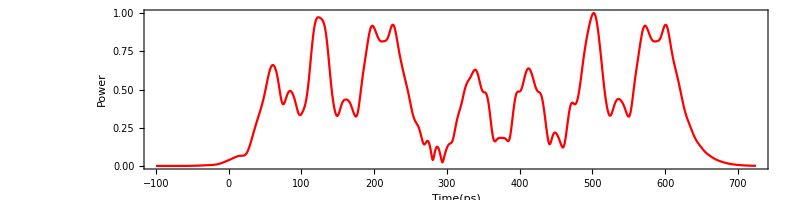

```mathematica
maxsig=Max[Table[{Abs[after[m]]},{m,1,25*bit+100,samp}]];
aftersig2=Table[{m,Abs[after[m]]/maxsig},{m,-100,25*bit+100,samp}];
ListLinePlot[aftersig2,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,PlotRange->{0,1},ImageSize->800]
```

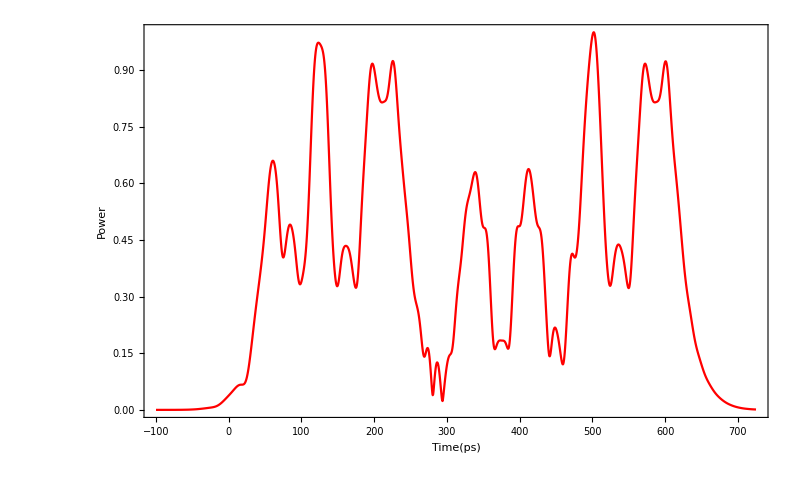

```mathematica
maxsig=Max[Table[{Abs[after[m]]},{m,1,25*bit+100,samp}]];
aftersig2=Table[{m,Abs[after[m]]/maxsig},{m,-100,25*bit+100,samp}];
ListLinePlot[aftersig2,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},PlotRange->{0,1},ImageSize->800]
```

## Eye Pattern

```mathematica
For[i=0.,i<=25*bit,i=i+samp,eyetime[i]=Mod[i,50]]
```

```mathematica
Print["Eye is ",(bit*25)/50]
```

Eye is 25/2

```mathematica
Table[eyetime[m],{m,0,25*bit,samp}];
```

```mathematica
eyebf=Table[{eyetime[m],nrzsig2[m+12.5]},{m,0,25*bit-12.5,samp}];
eyeaf=Table[{eyetime[m],Abs[after[m+12.5]]/maxsig},{m,0,25*bit-12.5,samp}];
```

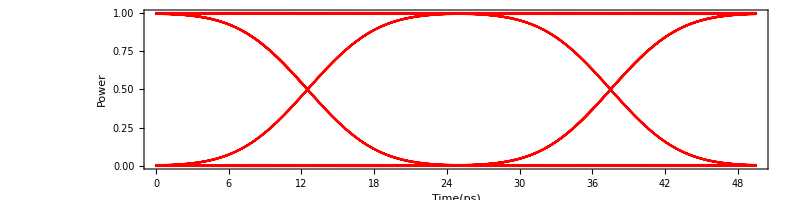

```mathematica
ListLinePlot[eyebf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

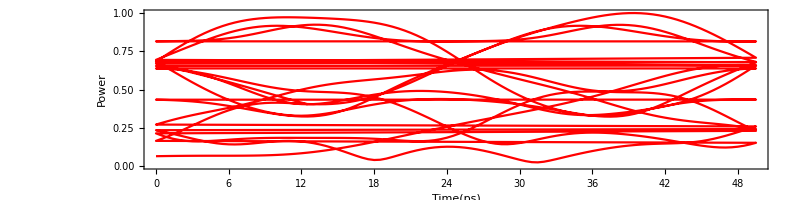

```mathematica
ListLinePlot[eyeaf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

## Bit Error Rate

```mathematica
For[m=22.5,m≤27.5,m=m+samp,For[i=m*2+1;j=1,i<= (bit*25-12.5)*1/samp,i=i+50*1/samp;j++,Subscript[list, m][j]=Part[eyeaf[[All,2]],i]]]
```

```mathematica
For[j=22.5;m=1;n=1;l0=0;l1=0,j≤27.5,j=j+samp,For[i=1,i≤(bit*25)/50,i++,
If[Subscript[list, j][i]>0.5,eye1[m]=Subscript[list, j][i];m++;l1=l1+1];
If[Subscript[list, j][i]<0.5,eye0[n]=Subscript[list, j][i];n++;l0=l0+1]]]
```

```mathematica
Print["1 is ",l1," point"]
Print["0 is ",l0," point"]
```

1 is 66 point

0 is 66 point

```mathematica
Table[eye1[m],{m,1,l1,1}];
Table[eye0[m],{m,1,l0,1}];
ave1=Sum[eye1[i],{i,1,l1}]/l1;
ave0=Sum[eye0[i],{i,1,l0}]/l0;
```

```mathematica
Print["Average of 1 is ",ave1]
Print["Average of 0 is ",ave0]
```

Average of 1 is 0.697744

Average of 0 is 0.289843

```mathematica
disp1=√(Sum[(eye1[i]-ave1)^2,{i,1,l1}]/l1);
disp0=√(Sum[(eye0[i]-ave0)^2,{i,1,l0}]/l0);
```

```mathematica
Print["A Standard Deviation of 1 is ",disp1]
Print["A Standard Deviation of 0 is ",disp0]
```

A Standard Deviation of 1 is 0.0746356

A Standard Deviation of 0 is 0.128666

```mathematica
gauss1[x_]:=1/(√(2*Pi*disp1^2))*Exp[-1/2*((x-ave1)/disp1^2)^2];
gauss0[x_]:=1/(√(2*Pi*disp0^2))*Exp[-1/2*((x-ave0)/disp0^2)^2];
```

General::munfl: Exp[-7844.26]は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

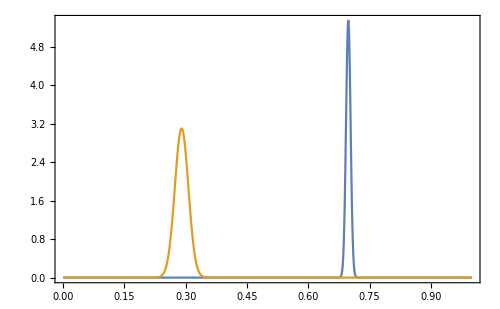

```mathematica
Plot[{gauss1[x],gauss0[x]},{x,0,1},PlotRange->All,Frame->True,ImageSize->500]
```

```mathematica
Q=(ave1-ave0)/(disp1+disp0);
Qdb=20Log10[Q];
Print["Q-factor is ",Q]
Print["Q-dB is ",Qdb," dB"]
```

Q-factor is 2.00638

Q-dB is 6.04827 dB

```mathematica
ber[x_]:=1/2*Erfc[x/(√2)];
Eyeopening=((ave1-disp1)-(ave0+disp0))/(ave1-ave0);
Print["Bit Error Rate is ",ber[Q]]
Print["Eye Opening is ",Eyeopening]
```

Bit Error Rate is 0.0224077

Eye Opening is 0.501591

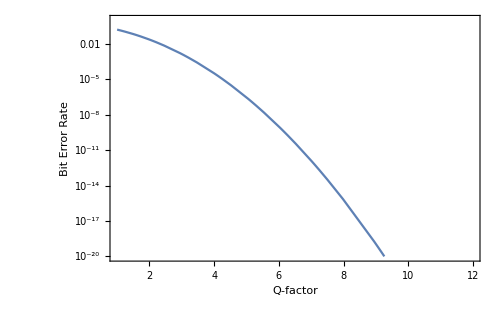

```mathematica
LogPlot[ber[z],{z,1,100},PlotRange->{{1,12},{10^-20,1}},Frame->True,FrameLabel->{"Q-factor","Bit Error Rate"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},ImageSize->500]
```